```mathematica
RcB[γ0_,q_,k_,R_]:=1/6 ((2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (2 k q Cos[k R] Sin[q R]^2-1/2 Sin[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))+3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (Sin[k R] (k^2+q^2-k^2 R^2-q^2 R^2-16 k^2 q^2 R^2+8 q^4 R^2+8 k^2 q^2 R^4-8 q^4 R^4-24 k^2 q^2 R γ0+16 q^4 R γ0+16 k^2 q^2 R^3 γ0-16 q^4 R^3 γ0-8 k^2 q^2 γ0^2+8 q^4 γ0^2+8 k^2 q^2 R^2 γ0^2-8 q^4 R^2 γ0^2-8 k^2 q^2 R (R+γ0) Cos[2 q R]+(k^2+q^2) (-1+R^2) Cos[4 q R]+4 k^2 q R Sin[2 q R]+8 q^3 R Sin[2 q R]-8 q^3 R^3 Sin[2 q R]+8 q^3 γ0 Sin[2 q R]-8 q^3 R^2 γ0 Sin[2 q R]+2 k^2 q R Sin[4 q R])+k Cos[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R]))))
IcB[γ0_,q_,k_,R_]:=((2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (-2 k q Sin[k R] Sin[q R]^2-1/2 Cos[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))-3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (k Sin[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])-2 Cos[k R] (-4 k^2 q^2 R (R+γ0) Cos[2 q R]+2 q (k^2 R-2 q^2 (-1+R^2) (R+γ0)) Sin[2 q R]-(k^2+q^2) (-1+R^2) Sin[2 q R]^2+q (4 q (R+γ0) (-q^2 (-1+R^2) (R+γ0)+k^2 (-2 R+R^3-γ0+R^2 γ0))+k^2 R Sin[4 q R])))));(*Wronskian[{RcB[γ0,q,k,R],IcB[γ0,q,k,R]},k]/(IcB[γ0,q,k,R]^2+RcB[γ0,q,k,R]^2)*)
```

0.866571

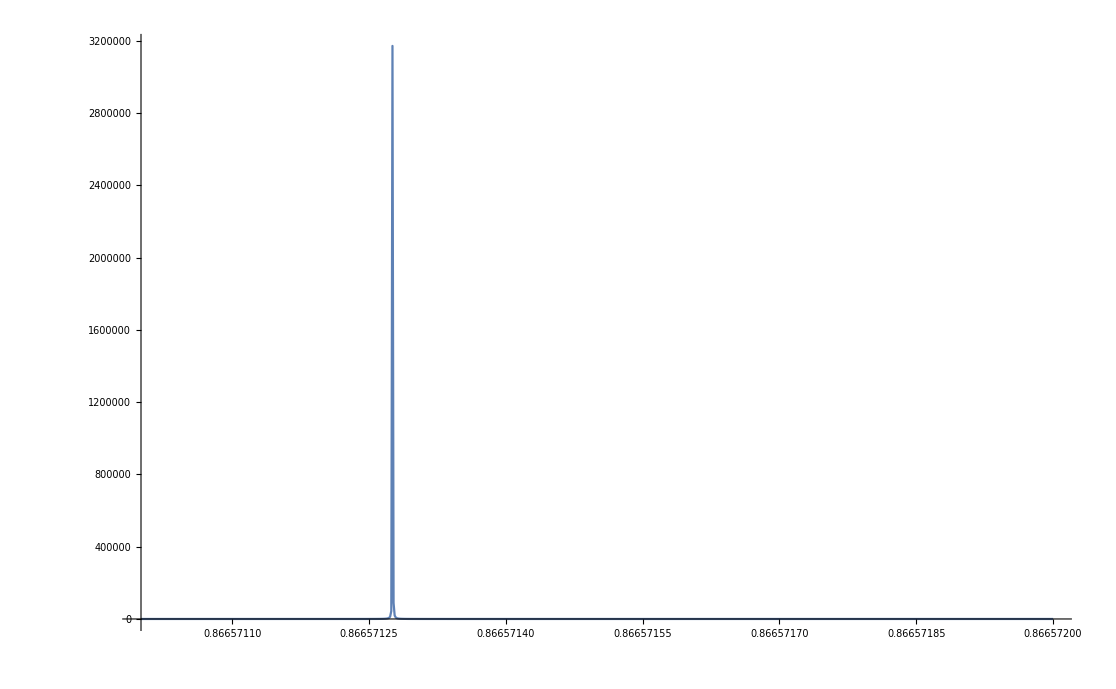

```mathematica
Δt[γ0_,q_,k_,R_]:=2k(((-3 k^3 R Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-27 k q^2 R Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k q^2 R^3 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k^3 q^2 R^3 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k q^4 R^3 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k q^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k q^2 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+48 k^3 q^2 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-48 k q^4 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k^3 q^2 R γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k q^4 R γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k q^2 R Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k q^2 R^3 Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k q^2 γ0 Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k q^2 R^2 γ0 Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+3 k^3 R Cos[k R] Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+3 k q^2 R Cos[k R] Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+3 k^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+3 q^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 k^2 R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 q^2 R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-48 k^2 q^2 R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 q^4 R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k^2 q^2 R^4 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 q^4 R^4 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-72 k^2 q^2 R γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+48 q^4 R γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+48 k^2 q^2 R^3 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-48 q^4 R^3 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^2 q^2 γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 q^4 γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k^2 q^2 R^2 γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 q^4 R^2 γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^2 q^2 R^2 Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^2 q^2 R γ0 Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 k^2 Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 q^2 Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+3 k^2 R^2 Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+3 q^2 R^2 Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^2 q^2 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+8 k^4 q^2 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+24 q^4 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-8 k^2 q^4 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+8 k^2 q^2 R^6 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-8 q^4 R^6 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-48 k^2 q^2 R^3 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+16 k^4 q^2 R^3 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+48 q^4 R^3 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-16 k^2 q^4 R^3 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+16 k^2 q^2 R^5 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-16 q^4 R^5 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-24 k^2 q^2 R^2 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+8 k^4 q^2 R^2 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+24 q^4 R^2 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-8 k^2 q^4 R^2 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]+8 k^2 q^2 R^4 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-8 q^4 R^4 γ0^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R]-48 k q^2 R^3 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2+16 k^3 q^2 R^3 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2+16 k q^2 R^5 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2-48 k q^2 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2+16 k^3 q^2 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2+16 k q^2 R^4 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2-12 k q Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+12 k q R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+24 k q^3 R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+24 k q^3 R γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+12 k^2 q R Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]+24 q^3 R Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]-24 q^3 R^3 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]+24 q^3 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]-24 q^3 R^2 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]+24 q^3 R^3 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]-8 k^2 q^3 R^3 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]-8 q^3 R^5 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]+24 q^3 R^2 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]-8 k^2 q^3 R^2 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]-8 q^3 R^4 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]-24 k q R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2 Sin[2 q R]+8 k^3 q R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2 Sin[2 q R]+8 k q R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[q R]^2 Sin[2 q R]+6 k^2 R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2-2 k^4 R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2+6 q^2 R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2-2 k^2 q^2 R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2-2 k^2 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2-2 q^2 R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[2 q R]^2+6 k q Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[4 q R]-6 k q R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[4 q R]+6 k^2 q R Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[4 q R]) (4 k R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (-2 k q Sin[k R] Sin[q R]^2-1/2 Cos[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))+2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (-2 k q R Cos[k R] Sin[q R]^2-2 q Sin[k R] Sin[q R]^2-1/2 Cos[k R] (-4 k q (R+γ0)+2 k Sin[2 q R])+1/2 R Sin[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))-3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (k (-2 k R+16 k q^2 R^3+32 k q^2 R^2 γ0+16 k q^2 R γ0^2+2 k R Cos[4 q R]) Sin[k R]+k R Cos[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])+Sin[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])-2 Cos[k R] (-8 k q^2 R (R+γ0) Cos[2 q R]+4 k q R Sin[2 q R]-2 k (-1+R^2) Sin[2 q R]^2+q (8 k q (R+γ0) (-2 R+R^3-γ0+R^2 γ0)+2 k R Sin[4 q R]))+2 R Sin[k R] (-4 k^2 q^2 R (R+γ0) Cos[2 q R]+2 q (k^2 R-2 q^2 (-1+R^2) (R+γ0)) Sin[2 q R]-(k^2+q^2) (-1+R^2) Sin[2 q R]^2+q (4 q (R+γ0) (-q^2 (-1+R^2) (R+γ0)+k^2 (-2 R+R^3-γ0+R^2 γ0))+k^2 R Sin[4 q R])))+3/4 k (k Sin[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])-2 Cos[k R] (-4 k^2 q^2 R (R+γ0) Cos[2 q R]+2 q (k^2 R-2 q^2 (-1+R^2) (R+γ0)) Sin[2 q R]-(k^2+q^2) (-1+R^2) Sin[2 q R]^2+q (4 q (R+γ0) (-q^2 (-1+R^2) (R+γ0)+k^2 (-2 R+R^3-γ0+R^2 γ0))+k^2 R Sin[4 q R]))) Derivative[1,0,0][Hypergeometric1F1][1/4 (3-k^2-R^2),3/2,R^2]-k R^2 (-3+k^2+R^2) (2 q (R+γ0)+Sin[2 q R]) (-2 k q Sin[k R] Sin[q R]^2-1/2 Cos[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R])) Derivative[1,0,0][Hypergeometric1F1][1/4 (7-k^2-R^2),5/2,R^2])-(-48 k^2 q^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 q^4 R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k^2 q^2 R^4 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 q^4 R^4 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-72 k^2 q^2 R γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+48 q^4 R γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+48 k^2 q^2 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-48 q^4 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k^2 q^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 q^4 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]+24 k^2 q^2 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 q^4 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k^2 q^2 R^2 Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k^2 q^2 R γ0 Cos[k R] Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2]-24 k^2 q^2 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+8 k^4 q^2 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+24 q^4 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-8 k^2 q^4 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+8 k^2 q^2 R^6 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-8 q^4 R^6 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-48 k^2 q^2 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+16 k^4 q^2 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+48 q^4 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-16 k^2 q^4 R^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+16 k^2 q^2 R^5 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-16 q^4 R^5 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-24 k^2 q^2 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+8 k^4 q^2 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+24 q^4 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-8 k^2 q^4 R^2 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+8 k^2 q^2 R^4 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]-8 q^4 R^4 γ0^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2]+3 k^3 R Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+27 k q^2 R Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k q^2 R^3 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^3 q^2 R^3 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k q^4 R^3 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k q^2 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k q^2 R^2 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-48 k^3 q^2 R^2 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+48 k q^4 R^2 γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k^3 q^2 R γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k q^4 R γ0^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k q^2 R Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k q^2 R^3 Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-24 k q^2 γ0 Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+24 k q^2 R^2 γ0 Cos[2 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 k^3 R Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]-3 k q^2 R Cos[4 q R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R]+48 k q^2 R^3 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2-16 k^3 q^2 R^3 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2-16 k q^2 R^5 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2+48 k q^2 R^2 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2-16 k^3 q^2 R^2 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2-16 k q^2 R^4 γ0 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2+12 k^2 q R Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+24 q^3 R Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]-24 q^3 R^3 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+24 q^3 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]-24 q^3 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]+24 q^3 R^3 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]-8 k^2 q^3 R^3 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]-8 q^3 R^5 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]+24 q^3 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]-8 k^2 q^3 R^2 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]-8 q^3 R^4 γ0 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]+12 k q Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]-12 k q R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]-24 k q^3 R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]-24 k q^3 R γ0 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[2 q R]+24 k q R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2 Sin[2 q R]-8 k^3 q R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2 Sin[2 q R]-8 k q R^4 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[k R] Sin[q R]^2 Sin[2 q R]+6 k^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]^2+6 q^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]^2-6 k^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]^2-6 q^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[2 q R]^2+6 k^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2-2 k^4 R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2+6 q^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2-2 k^2 q^2 R^2 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2-2 k^2 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2-2 q^2 R^4 Cos[k R] Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] Sin[2 q R]^2+6 k^2 q R Cos[k R] Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[4 q R]-6 k q Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[4 q R]+6 k q R^2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] Sin[k R] Sin[4 q R]) (2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (2 q Cos[k R] Sin[q R]^2-2 k q R Sin[k R] Sin[q R]^2-1/2 Sin[k R] (-4 k q (R+γ0)+2 k Sin[2 q R])-1/2 R Cos[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))+4 k R^2 Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (2 k q Cos[k R] Sin[q R]^2-1/2 Sin[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))+3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (k Cos[k R] (-2 k R+16 k q^2 R^3+32 k q^2 R^2 γ0+16 k q^2 R γ0^2+2 k R Cos[4 q R])+Sin[k R] (2 k-2 k R^2-32 k q^2 R^2+16 k q^2 R^4-48 k q^2 R γ0+32 k q^2 R^3 γ0-16 k q^2 γ0^2+16 k q^2 R^2 γ0^2-16 k q^2 R (R+γ0) Cos[2 q R]+2 k (-1+R^2) Cos[4 q R]+8 k q R Sin[2 q R]+4 k q R Sin[4 q R])+R Cos[k R] (k^2+q^2-k^2 R^2-q^2 R^2-16 k^2 q^2 R^2+8 q^4 R^2+8 k^2 q^2 R^4-8 q^4 R^4-24 k^2 q^2 R γ0+16 q^4 R γ0+16 k^2 q^2 R^3 γ0-16 q^4 R^3 γ0-8 k^2 q^2 γ0^2+8 q^4 γ0^2+8 k^2 q^2 R^2 γ0^2-8 q^4 R^2 γ0^2-8 k^2 q^2 R (R+γ0) Cos[2 q R]+(k^2+q^2) (-1+R^2) Cos[4 q R]+4 k^2 q R Sin[2 q R]+8 q^3 R Sin[2 q R]-8 q^3 R^3 Sin[2 q R]+8 q^3 γ0 Sin[2 q R]-8 q^3 R^2 γ0 Sin[2 q R]+2 k^2 q R Sin[4 q R])+Cos[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])-k R Sin[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R]))-3/4 k (Sin[k R] (k^2+q^2-k^2 R^2-q^2 R^2-16 k^2 q^2 R^2+8 q^4 R^2+8 k^2 q^2 R^4-8 q^4 R^4-24 k^2 q^2 R γ0+16 q^4 R γ0+16 k^2 q^2 R^3 γ0-16 q^4 R^3 γ0-8 k^2 q^2 γ0^2+8 q^4 γ0^2+8 k^2 q^2 R^2 γ0^2-8 q^4 R^2 γ0^2-8 k^2 q^2 R (R+γ0) Cos[2 q R]+(k^2+q^2) (-1+R^2) Cos[4 q R]+4 k^2 q R Sin[2 q R]+8 q^3 R Sin[2 q R]-8 q^3 R^3 Sin[2 q R]+8 q^3 γ0 Sin[2 q R]-8 q^3 R^2 γ0 Sin[2 q R]+2 k^2 q R Sin[4 q R])+k Cos[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])) Derivative[1,0,0][Hypergeometric1F1][1/4 (3-k^2-R^2),3/2,R^2]-k R^2 (-3+k^2+R^2) (2 q (R+γ0)+Sin[2 q R]) (2 k q Cos[k R] Sin[q R]^2-1/2 Sin[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R])) Derivative[1,0,0][Hypergeometric1F1][1/4 (7-k^2-R^2),5/2,R^2]))/(12 (1/36 (2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (2 k q Cos[k R] Sin[q R]^2-1/2 Sin[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))+3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (Sin[k R] (k^2+q^2-k^2 R^2-q^2 R^2-16 k^2 q^2 R^2+8 q^4 R^2+8 k^2 q^2 R^4-8 q^4 R^4-24 k^2 q^2 R γ0+16 q^4 R γ0+16 k^2 q^2 R^3 γ0-16 q^4 R^3 γ0-8 k^2 q^2 γ0^2+8 q^4 γ0^2+8 k^2 q^2 R^2 γ0^2-8 q^4 R^2 γ0^2-8 k^2 q^2 R (R+γ0) Cos[2 q R]+(k^2+q^2) (-1+R^2) Cos[4 q R]+4 k^2 q R Sin[2 q R]+8 q^3 R Sin[2 q R]-8 q^3 R^3 Sin[2 q R]+8 q^3 γ0 Sin[2 q R]-8 q^3 R^2 γ0 Sin[2 q R]+2 k^2 q R Sin[4 q R])+k Cos[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])))^2+(2 R^2 (-3+k^2+R^2) Hypergeometric1F1[1/4 (7-k^2-R^2),5/2,R^2] (2 q (R+γ0)+Sin[2 q R]) (-2 k q Sin[k R] Sin[q R]^2-1/2 Cos[k R] (2 q (-k^2+q^2) (R+γ0)+(k^2+q^2) Sin[2 q R]))-3/2 Hypergeometric1F1[1/4 (3-k^2-R^2),3/2,R^2] (k Sin[k R] (-k^2 R-9 q^2 R+8 q^2 R^3+8 k^2 q^2 R^3-8 q^4 R^3-8 q^2 γ0+8 q^2 R^2 γ0+16 k^2 q^2 R^2 γ0-16 q^4 R^2 γ0+8 k^2 q^2 R γ0^2-8 q^4 R γ0^2-8 q^2 (-1+R^2) (R+γ0) Cos[2 q R]+(k^2+q^2) R Cos[4 q R]-4 q Sin[2 q R]+4 q R^2 Sin[2 q R]+8 q^3 R^2 Sin[2 q R]+8 q^3 R γ0 Sin[2 q R]+2 q Sin[4 q R]-2 q R^2 Sin[4 q R])-2 Cos[k R] (-4 k^2 q^2 R (R+γ0) Cos[2 q R]+2 q (k^2 R-2 q^2 (-1+R^2) (R+γ0)) Sin[2 q R]-(k^2+q^2) (-1+R^2) Sin[2 q R]^2+q (4 q (R+γ0) (-q^2 (-1+R^2) (R+γ0)+k^2 (-2 R+R^3-γ0+R^2 γ0))+k^2 R Sin[4 q R]))))^2)))
0.8665705594569907

Plot[Δt[1,0.866571,k,4],{k,0.866571,0.866572},PlotRange->Full,PlotPoints->400,TicksStyle->Large]
```